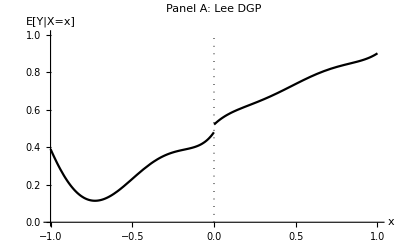

```mathematica
tauY=0.52-0.48;
beta0Yr=0.52;
beta0Yl=0.48;
beta1Yr=0.84;
beta1Yl=1.27;
beta2Yr=-3.00;
beta2Yl=7.18;
beta3Yr=7.99;
beta3Yl=20.21;
beta4Yr=-9.01;
beta4Yl=21.54;
beta5Yr=3.56;
beta5Yl=7.33;

fl[x_]:=beta0Yl+beta1Yl x+beta2Yl x^2+beta3Yl x^3+beta4Yl x^4+beta5Yl x^5;
fr[x_]:=beta0Yr+beta1Yr x+beta2Yr x^2+beta3Yr x^3+beta4Yr x^4+beta5Yr x^5;

vertical=Line[{{0,0},{0,1}}];
DGPLee=Plot[Piecewise[{{fl[x],x<0},{fr[x],x>0}}],{x,-1,1},
	PlotStyle-> {Black},
	PlotLabel-> "Panel A: Lee DGP",
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[Y|X=x]"},
	AxesOrigin->{-1,0},
	PlotRange->{{-1,1},{0,1}},
	Epilog->{Directive[Dotted],vertical}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RD DGP Lee.pdf",DGPLee, ImageSize->Medium];
```